## Solar Neutrino Flux

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ryanplestid/Research/Physics_Projects/Archived_Projects/Solar-Upscatter/Mathematica/Paper-II-clean

All normalizations taken from https://arxiv.org/pdf/1104.1639.pdf

All imported flux shapes are normalized to one.

```mathematica
pp=({#⟦1⟧,6.03 10^10#⟦2⟧}&)/@Import["SolarNuFlux/pp.dat"];
n13=({#⟦1⟧,2.17 10^8#⟦2⟧}&)/@Import["SolarNuFlux/n13.dat"];
o15=({#⟦1⟧,1.56 10^8#⟦2⟧}&)/@Import["SolarNuFlux/o15.dat"];
f17=({#⟦1⟧,3.4 10^6#⟦2⟧}&)/@Import["SolarNuFlux/f17.dat"];
b8=({#⟦1⟧,4.59 10^6#⟦2⟧}&)/@Import["SolarNuFlux/b8.dat"];
hep=({#⟦1⟧,8.31 10^3#⟦2⟧}&)/@Import["SolarNuFlux/hep.dat"];
be7gs=({10^-3#⟦1⟧+0.8613,4.56 10^9#⟦2⟧}&)/@Import["SolarNuFlux/7be-gs.dat"];
be7ex=({10^-3#⟦1⟧+0.3843,4 10^8#⟦2⟧}&)/@Import["SolarNuFlux/7be-ex.dat"];
```

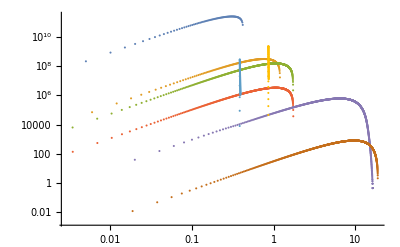

```mathematica
ListLogLogPlot[{pp,n13,o15,f17,b8,hep,be7ex,be7gs}]
```

```mathematica
MyDelta[x_,σ_]:= 1/(√(2π σ^2))Exp[-1/2 x^2/σ^2];
CutOff[x_,y_]:=UnitStep[y-x];interp=(  Interpolation[#,InterpolationOrder->1][Eν]CutOff[Eν,Last[#]⟦1⟧] &);
```

```mathematica
ppx =interp @ pp;
n13x =interp @ n13;
o15x= interp @ o15;
f17x=interp @ f17;
b8x=interp@ b8;
hepx=interp @ hep;
be7gsx=4.56 10^9 MyDelta[Eν-0.8613,0.01];
be7exx=4 10^8 MyDelta[Eν-0.3843,0.01];
pepx=1.5 10^8 MyDelta[Eν-1.44,0.01];
```

```mathematica
SolarNuOfx=ppx+n13x+o15x+f17x+b8x+hepx+be7gsx+pepx;
```

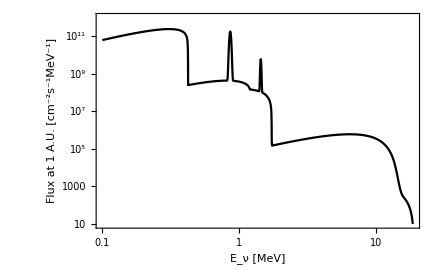

```mathematica
LogLogPlot[{SolarNuOfx},{Eν,0.1,20},PlotRange->{Automatic,{10,10^12}},Frame-> True,PlotTheme->"Monochrome",FrameLabel->(Style[#,14]&)/@{"E_ν [MeV]","Flux at 1 A.U. [cm^-2s^-1MeV^-1]"}]//Quiet
```

## Neutrino Spectrum after scattering

```mathematica
NIntegrate[SolarNuOfx,{Eν,0,20},Method->{"DoubleExponential","SymbolicProcessing"-> 0},AccuracyGoal->Infinity]//Quiet
NIntegrate[SolarNuOfx,{Eν,0,20},Method->{"Trapezoidal","SymbolicProcessing"-> 0},AccuracyGoal->Infinity]//Quiet
```

6.539×10^10

6.5388×10^10

```mathematica
NormSolarNuOfx=1/(6.538802954197485*10^10)SolarNuOfx;
```

```mathematica
σ=GF^2 Qw^2 (Eν^2 √(1-ϵ^2) (3-ϵ^2))/π/.ϵ-> mN/Eν;
σRed= (Eν^2 √(1-ϵ^2) (3-ϵ^2))/π/.ϵ-> mN/Eν//Simplify (* Red is for reduced*)
```

((3 Eν^2-mN^2) √(1-mN^2/Eν^2))/π

```mathematica
fluxHNL=NormSolarNuOfx σRed; 
eFrac=Interpolation[({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pee.dat"]][Eν];
μFrac=Interpolation[({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pem.dat"]][Eν];
τFrac=Interpolation[({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pet.dat"]][Eν];
fluxHNLUeN=eFrac NormSolarNuOfx σRed  1/(Eν √(1-mN^2/Eν^2))UnitStep[Eν-mN];
fluxHNLUμN=μFrac NormSolarNuOfx σRed 1/(Eν √(1-mN^2/Eν^2))UnitStep[Eν-mN];
fluxHNLUτN=τFrac NormSolarNuOfx σRed 1/(Eν √(1-mN^2/Eν^2))UnitStep[Eν-mN];
```

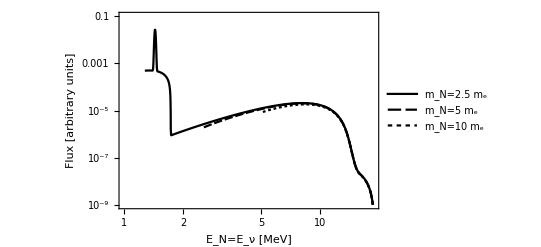

```mathematica
LogLogPlot[{fluxHNLUτN/.mN->  2.5 0.511,fluxHNLUτN/.mN->5 0.511,fluxHNLUτN/.mN->10 0.511},{Eν,1,20},Frame-> True, PlotTheme->"Monochrome",PlotLegends->Placed[{"m_N=2.5 m_e","m_N=5 m_e","m_N=10 m_e     "},{0.4,0.825}],FrameLabel->(Style[#,12]&)/@{"E_N=E_ν  [MeV]","Flux   [arbitrary units]"},FrameTicks->{Automatic,Automatic},PlotRange->{10^-9,10^-1}]//Quiet
```

```mathematica
Export["N-Spec/fluxHNLUeN.m",fluxHNLUeN]
Export["N-Spec/fluxHNLUμN.m",fluxHNLUμN]
Export["N-Spec/fluxHNLUτN.m",fluxHNLUτN]
```

N-Spec/fluxHNLUeN.m

N-Spec/fluxHNLUμN.m

N-Spec/fluxHNLUτN.m

```mathematica
fluxHNL=<||>;
flavours={"e","μ","τ"};
fluxHNL["e"]=fluxHNLUeN;
fluxHNL["μ"]=fluxHNLUμN;
fluxHNL["τ"]=fluxHNLUτN;
```